```mathematica
list=StringSplit[Import["~/changliu","Text"],"\n"];
```

```mathematica
json=Developer`ReadRawJSONString@#&/@list//Parallelize;
```

```mathematica
json=Select[json,#["data","message"]!="今日无成绩"&];
```

```mathematica
userIdList[n_]:=#["id"]&/@json[[n]]["data","result"];
```

```mathematica
userIdFromDayRecord[r_]:=#["userId"]&/@r;
```

```mathematica
results=#["data","result"]&/@json
```

```mathematica
userIdList=Flatten[userIdFromDayRecord/@results,1]
```

```mathematica
sorted=ReverseSortBy[Normal[CountsBy[userIdList,#&]],Values];
```

```mathematica
userInfoFromDayRecord[r_]:={#["userId"],#["userName"]}&/@r;
```

```mathematica
userInfoList=Flatten[userInfoFromDayRecord/@results,1]
```

```mathematica
findUsernameById[id_]:=Select[userInfoList,#[[1]]==id&]//DeleteDuplicates;
```

```mathematica
KeyMap[findUsernameById,Association[sorted]]//Parallelize
```

<|{{324,清凉爽口}}→1037,{{1078,lndlinger}}→893,{{470011,一个LSP}}→809,{{408,飘风}}→790,{{469750,符华上仙}}→622,{{975,古西尘}}→618,{{469713,GUB}}→574,{{1060,此方}}→505,{{821,矧可射思}}→470,{{851,十七七七七}}→446,{{471141,禧}}→415,{{828,我执}}→360,{{755,浪子}}→350,{{469723,幺幺零}}→341,{{82,E迅阿金}}→330,{{469623,Jiamian1}}→327,{{544,wangchao891128}}→303,{{471089,Apo110}}→296,{{904,一条牛}}→294,{{432,突突突}}→286,{{469663,BUG}}→281,{{470731,弹跳鲜虾滑}}→254,{{871,嘉}}→252,{{469853,按键伤人}}→243,{{362,萌新}}→234,{{470380,承让承让承让}}→227,{{796,冰冰}}→227,{{469753,bxi}}→213,{{276,我曾经是个冒险者}}→195,{{470145,打字机}}→194,{{370,谭宇}}→183,{{58,【零九】随风}}→183,{{471282,梦幻·罗嫣}}→179,{{404,靓仔来了}}→173,{{289,无影}}→166,{{470968,简单}}→162,{{214,君子乔}}→162,{{470418,18810103}}→160,{{227,夕夕夕沐丶}}→155,{{753,whitebird}}→153,{{471346,彩虹爱晗宝}}→149,{{469664,十七七七}}→147,{{471352,卑鄙的两脚兽}}→138,{{368,魔方}}→128,{{134,swat1027}}→127,{{862,韦少FTCL}}→123,{{490,ly363930610}}→123,{{470687,狼}}→122,{{290,无聊}}→121,{{469751,HY嘉}}→119,{{648,wuxigk}}→119,{{850,1477821167}}→118,{{471267,bczhc}}→117,{{358,茶味}}→111,{{339,百花}}→111,{{250,小涛清华}}→110,{{459,zhaozwf}}→109,{{1076,秋月}}→108,{{356,若晨}}→107,{{471464,b3}}→106,{{471239,華喵}}→105,{{470199,般若狼}}→103,{{900,1459233354}}→101,{{1015,lzf12233}}→100,{{594,bzwhjsw}}→100,{{470748,菜鸡}}→94,{{776,Limoya}}→93,{{604,吱吱}}→93,{{619,a497341787}}→90,{{247,小宇}}→90,{{470976,小旭}}→88,{{471195,b}}→85,{{111,LuoshuiTianyi}}→85,{{470284,冰凉可口}}→84,{{558,xihuanljx}}→84,{{471286,拉架珠地空气层}}→83,{{691,我爱喝牛奶}}→83,{{471441,---}}→80,{{988,南柯yi梦}}→80,{{470292,平静}}→79,{{688,石浅}}→78,{{582,chrdw}}→76,{{471274,092}}→73,{{675,七堇年丨浅易丶}}→72,{{167,三明治}}→72,{{471155,离}}→71,{{471547,c123}}→68,{{474,xlboy}}→68,{{647,917}}→66,{{634,悟空的小日记}}→66,{{471482,zxczxczxc}}→65,{{469706,learwang}}→63,{{469637,xdyy283306}}→62,{{639,歪歪}}→62,{{471147,键动我心}}→60,{{928,最佳演员}}→60,{{306,杨小草}}→60,{{471077,100字每分就好}}→59,{{469714,我静如镜}}→58,{{342,看海}}→58,{{470280,小鹤天下无敌}}→57,{{471385,破凤凰s}}→56,{{469861,灰菇凉}}→55,{{470721,RDpenguin}}→54,{{470641,玖柒}}→54,{{607,风萧萧}}→54,{{469924,胖墩儿}}→53,{{470165,周伯通}}→52,{{469786,qffffff}}→51,{{980,CurvedMirror}}→51,{{350,聆竹听风}}→50,{{286,斯拉雪麦格}}→50,{{470131,程序员周先生}}→49,{{471566,swwrww}}→48,{{471448,夜星}}→48,{{469877,三千里路云和月}}→48,{{469740,E迅-大儿童}}→48,{{471550,赢}}→46,{{469715,鱼想衣裳花想容}}→46,{{471389,阿嫣}}→45,{{212,号账}}→45,{{310,柚子}}→44,{{469734,青见}}→43,{{787,励志好年华}}→43,{{225,圈0o}}→43,{{470732,跑调键盘手}}→42,{{470552,MuKer}}→42,{{469651,鹏鹏}}→41,{{757,骑士}}→41,{{386,逍遥金鱼}}→40,{{154,yqyang79}}→40,{{471469,❽级大狂风}}→39,{{471244,81131567}}→39,{{470925,芋头}}→39,{{496,zhm_275}}→39,{{372,账号}}→39,{{929,1329590287}}→38,{{366,让心如水}}→38,{{469932,11111}}→37,{{443,小鱼儿}}→36,{{470923,LF3266}}→35,{{470352,爱如潮水}}→35,{{1,}}→35,{{471430,看我把伞}}→34,{{471272,福至心灵}}→34,{{471121,玄}}→34,{{470928,天不生我小随风}}→34,{{857,空论}}→34,{{137,Tony}}→34,{{666,西蒙}}→33,{{454,就是午啊}}→33,{{470792,cocoon}}→32,{{470648,尼古拉烟丝}}→32,{{470510,E迅阿虎}}→31,{{471402,丰华}}→30,{{809,qq81641080}}→30,{{730,新人菜鸟}}→30,{{298,木樨}}→30,{{1011,15838284366}}→29,{{663,小陈数码}}→29,{{405,风中追风}}→29,{{381,路人甲}}→29,{{471611,是花耶}}→28,{{471304,熊大大}}→28,{{471207,林煊}}→28,{{469683,一一一}}→28,{{469666,帝丝}}→28,{{1071,蛙仔}}→28,{{968,starry}}→28,{{316,榜眼}}→28,{{470071,子衡}}→27,{{234,太白}}→27,{{469731,chijichen}}→26,{{469680,kkoozz}}→26,{{469646,OwO}}→26,{{469842,SA}}→25,{{471624,陈小宇}}→24,{{526,小啊浩}}→24,{{392,金木}}→24,{{169,专注者}}→24,{{471082,Ethereal+Faith}}→23,{{471541,Kakarotto}}→22,{{470056,红米粉}}→22,{{469897,浪里个浪}}→22,{{469722,阿菠萝}}→22,{{471532,脚皮的皮}}→21,{{471087,wbbru}}→21,{{471050,芋头2}}→21,{{469783,ifss}}→21,{{439,Hotoo}}→21,{{471169,执傲}}→20,{{470869,爱言叶}}→20,{{471627,壴}}→19,{{471353,test01}}→19,{{470833,尚闫}}→19,{{470154,pony}}→19,{{470104,666}}→19,{{469701,贪玩的阳阳}}→19,{{919,紫电}}→19,{{438,55555}}→19,{{470845,hxd}}→18,{{470119,小指}}→18,{{291,昆廷}}→18,{{471480,All}}→17,{{470632,2646077977}}→17,{{469852,HY}}→17,{{999,DIAMOND}}→17,{{523,12358}}→17,{{397,陈桂花}}→17,{{144,wangt_upc}}→17,{{471306,槿绣}}→16,{{470836,须弥狼}}→16,{{470332,蓝源}}→16,{{469834,呵+呵}}→16,{{380,路人乙}}→16,{{471116,owenyang}}→15,{{469992,櫐櫐}}→15,{{469939,wuhaojushi}}→15,{{1019,信仰}}→15,{{944,我想你}}→15,{{636,谭巨浪}}→15,{{147,wrey}}→15,{{471538,pea_snow}}→14,{{471361,分分过}}→14,{{470779,lhl}}→14,{{470217,小忧忧}}→14,{{470021,fujiale}}→14,{{469994,1355728038}}→14,{{469984,milando}}→14,{{469864,淫僧}}→14,{{469830,雪之下雪乃}}→14,{{1049,小杨}}→14,{{1041,raines}}→14,{{870,花梦楼主}}→14,{{854,qeszxc}}→14,{{840,145923354}}→14,{{724,Zeropo}}→14,{{351,肿泽}}→14,{{471613,秋名山}}→13,{{471100,Xipo}}→13,{{470749,简单男孩}}→13,{{469791,小兔﹑卟乖乖}}→13,{{1033,简单幸福}}→13,{{515,朝茶}}→13,{{231,天南星}}→13,{{139,vicsonyang}}→13,{{138,VcWw}}→13,{{125,shallow88888}}→13,{{471533,shy}}→12,{{470820,夜雨孤鸿}}→12,{{470403,Faker}}→12,{{470020,penpel}}→12,{{469841,zhixiao}}→12,{{469804,一只没有梦想的咸鱼}}→12,{{469768,2849276812}}→12,{{817,终不似少年游}}→12,{{783,2123603545@qq.com}}→12,{{718,我不是鄙人}}→12,{{359,荀攸-小鹤音形}}→12,{{471263,死鬼}}→11,{{471144,蛋挞}}→11,{{470981,Ryoku}}→11,{{470859,鱼丸}}→11,{{470152,Balazar}}→11,{{469922,街头传说}}→11,{{469865,momijineko}}→11,{{469618,左轮诗人}}→11,{{1012,Impel}}→11,{{831,tyx}}→11,{{790,看-海都是水}}→11,{{449,汪叽}}→11,{{242,小丁}}→11,{{471023,此此此此方}}→10,{{470583,E迅阿哲}}→10,{{470235,A+bull}}→10,{{469873,极速的忧伤}}→10,{{1048,melo}}→10,{{848,910961200}}→10,{{815,嶔崟}}→10,{{678,砂糖}}→10,{{613,lk}}→10,{{416,黄大大}}→10,{{409,香儿飞飞}}→10,{{343,破凤凰}}→10,{{101,larrylinli}}→10,{{471632,卡}}→9,{{471569,银古}}→9,{{471280,15137170417}}→9,{{471208,卢瑟}}→9,{{470226,那小孩也很帅}}→9,{{470202,代号：重打}}→9,{{470157,黑桃匕首}}→9,{{470038,骚浪贱}}→9,{{469961,Vas}}→9,{{469810,csource}}→9,{{1051,白小焦}}→9,{{867,icefrog}}→9,{{863,何乐}}→9,{{849,莫比乌斯}}→9,{{782,xx363930610}}→9,{{535,3190214683}}→9,{{312,栗子}}→9,{{69,aspire102}}→9,{{4,0225}}→9,{{471472,海七}}→8,{{471348,Y1688}}→8,{{471175,无他}}→8,{{470581,1137257746}}→8,{{470556,yhhc}}→8,{{470451,crea0618}}→8,{{470410,你是来拉屎的吧？}}→8,{{470168,我是一朵花}}→8,{{469899,rurudo}}→8,{{469898,小鹤练习生}}→8,{{1083,B1aze}}→8,{{628,魏东}}→8,{{610,烟刀}}→8,{{423,FiveLaaLi}}→8,{{199,初心-小鹤纯双}}→8,{{118,qianxue}}→8,{{13,123}}→8,{{471339,嫣然}}→7,{{471303,美琴酱}}→7,{{471128,简单少年}}→7,{{470980,简单女孩}}→7,{{470463,liskrbai}}→7,{{470318,王总越来越好玩}}→7,{{470271,韭菜}}→7,{{469845,forpchu}}→7,{{469808,疫苗}}→7,{{469727,青柠}}→7,{{469724,乌衣}}→7,{{954,招财猫}}→7,{{893,键来}}→7,{{883,千里}}→7,{{723,祭}}→7,{{603,瓜田}}→7,{{491,czning}}→7,{{395,阿华}}→7,{{232,天王小渣渣}}→7,{{471519,a798291284}}→6,{{471463,b2}}→6,{{471336,冬日午后}}→6,{{471256,一群LSP}}→6,{{471221,114514}}→6,{{471076,mishiwa}}→6,{{470839,冰清玉洁烂裤裆}}→6,{{470716,暗黑丸山彩}}→6,{{470658,浪小稽}}→6,{{470521,q425624322}}→6,{{470247,乔木木}}→6,{{470051,暗影}}→6,{{470029,renjiji123456}}→6,{{469968,一抹泪花}}→6,{{469914,Shanoa}}→6,{{469874,深蓝}}→6,{{469710,阿菠萝的幺幺零}}→6,{{1022,键神一笑}}→6,{{1020,f274819002}}→6,{{820,你明白吗}}→6,{{645,一头有梦想的驴}}→6,{{537,细水长流}}→6,{{434,老套}}→6,{{307,枫叶}}→6,{{81,Ericvictor}}→6,{{14,123456}}→6,{{471656,是花哦}}→5,{{471554,心}}→5,{{471416,疫苗纯单}}→5,{{471399,紫钰情深}}→5,{{471229,吉良吉影}}→5,{{471007,呆呆}}→5,{{470788,草田先生}}→5,{{470643,caifa}}→5,{{470406,binv}}→5,{{470257,w104426424}}→5,{{470186,耶稣和观音恋爱}}→5,{{470183,dineryaf}}→5,{{470039,yyzk}}→5,{{469959,不要以为你赢了}}→5,{{469625,飘风小号}}→5,{{1005,张涛}}→5,{{974,千空}}→5,{{912,ankit114}}→5,{{899,何世恒}}→5,{{756,易平12}}→5,{{713,神键手}}→5,{{689,QQ碎冰冰}}→5,{{673,李成}}→5,{{667,sky}}→5,{{516,3777280}}→5,{{488,毁灭欲}}→5,{{427,E迅阿党}}→5,{{399,雁子}}→5,{{369,谭八风}}→5,{{257,小镜子}}→5,{{239,守候}}→5,{{191,六月的雨}}→5,{{173,为何有雨}}→5,{{164,丁丁}}→5,{{120,qwxying}}→5,{{59,930018003}}→5,{{471615,卡农卡农}}→4,{{471601,星空不见}}→4,{{471591,我能跟上}}→4,{{471581,123123}}→4,{{471546,1601527345}}→4,{{471188,今晚打老鼠}}→4,{{471185,vsama}}→4,{{471139,麸子与米糠}}→4,{{471105,tjy09160723}}→4,{{471035,邹佳}}→4,{{470983,coder}}→4,{{470960,谦}}→4,{{470899,3063827816}}→4,{{470722,旅行者1号}}→4,{{470569,sbqsbqsbq}}→4,{{470534,艾s}}→4,{{470439,狂淦}}→4,{{470059,光光光光方}}→4,{{470057,50994586}}→4,{{469986,EDDIE}}→4,{{469910,霡霂阡陌}}→4,{{469901,o(=•ェ•=)m}}→4,{{469900,会打字的橘猫}}→4,{{469840,青蛙_FROG}}→4,{{469747,秦淮}}→4,{{469658,yungts}}→4,{{964,thevoid}}→4,{{946,高手}}→4,{{916,德玛西亚猫咪}}→4,{{710,溪林居士}}→4,{{570,xiao}}→4,{{548,幻羽}}→4,{{513,ac233}}→4,{{495,1552654917}}→4,{{320,沉石}}→4,{{294,晓览}}→4,{{254,小福}}→4,{{230,大雄}}→4,{{130,shutao}}→4,{{70,changan}}→4,{{471641,梦终空}}→3,{{471607,H+cool}}→3,{{471446,喵呜呼呼}}→3,{{471341,阿刁}}→3,{{471335,好热}}→3,{{471329,muker114514}}→3,{{471324,yanyang}}→3,{{471309,罗嫣小号}}→3,{{471059,小虎队：斩浪}}→3,{{470999,镜}}→3,{{470728,white}}→3,{{470602,MUKER的小号}}→3,{{470496,lian}}→3,{{470448,向流年}}→3,{{470370,让我载次文吧}}→3,{{470340,小鹤牛方}}→3,{{470261,剑影斑驳}}→3,{{470222,帕德玛刚玉}}→3,{{470201,knahknah}}→3,{{470177,gsyp20001}}→3,{{470174,舞魔棍}}→3,{{470149,死宅}}→3,{{470084,tan@jaka}}→3,{{470068,没有意义}}→3,{{470061,35416086@qq.com}}→3,{{469996,28948486205}}→3,{{469995,打打更健康}}→3,{{469956,英雄616}}→3,{{469908,2016494896}}→3,{{469885,水中月}}→3,{{469869,一条牛の小鹤音形}}→3,{{469796,ufm1xk1}}→3,{{469692,呆呆papa}}→3,{{469671,6683}}→3,{{1068,打到第一就收手}}→3,{{1056,Xiaohei.Meng}}→3,{{1002,121321996}}→3,{{969,erosyun}}→3,{{947,荒木}}→3,{{934,迟到的叛逆}}→3,{{903,来将可留姓名}}→3,{{879,花千骨}}→3,{{878,流流}}→3,{{876,罗嫣}}→3,{{866,WJXi}}→3,{{865,ToTo}}→3,{{725,莽夫}}→3,{{641,liumeng260}}→3,{{573,mono}}→3,{{563,皇粉粉}}→3,{{524,万字诀}}→3,{{510,恩赐解脱}}→3,{{424,造梦}}→3,{{344,红江}}→3,{{314,栗子——小鹤双拼}}→3,{{309,柏原崇女盆友}}→3,{{213,君君的新想法}}→3,{{209,友大人}}→3,{{202,前方}}→3,{{196,刘尼尔}}→3,{{194,凌乱}}→3,{{90,gendaceshi1}}→3,{{471670,Kyro}}→2,{{471636,大海}}→2,{{471548,团团圆圆}}→2,{{471470,loxndp}}→2,{{471466,禧禧}}→2,{{471462,b1}}→2,{{471422,hu896166912}}→2,{{471412,学海}}→2,{{471357,test05}}→2,{{471355,test03}}→2,{{471294,辣条}}→2,{{471264,测试帐号}}→2,{{471248,+}}→2,{{471235,原}}→2,{{471219,艾克}}→2,{{471217,namr}}→2,{{471127,是花啊}}→2,{{471095,lyz}}→2,{{471074,Xashian}}→2,{{471024,此此方}}→2,{{470977,菜β}}→2,{{470947,哟西哟西}}→2,{{470819,麻风·国王}}→2,{{470809,a1914}}→2,{{470808,大谢小鹤369}}→2,{{470782,hhyycc}}→2,{{470724,1048271711@qq.com}}→2,{{470680,弱鸡}}→2,{{470631,Dagger}}→2,{{470572,魏子遇}}→2,{{470568,2992107204}}→2,{{470488,1239636115}}→2,{{470479,静如心水}}→2,{{470474,水心如静}}→2,{{470469,静水如心}}→2,{{470449,如水心静}}→2,{{470442,紫钰情深-86五笔}}→2,{{470366,lv4664}}→2,{{470344,拉了个大的}}→2,{{470236,铲屎官Jocker}}→2,{{470142,wan1396138}}→2,{{470110,崔巍Z}}→2,{{470095,sm}}→2,{{470062,WS53}}→2,{{469987,hxlwd123}}→2,{{469975,hello_ik}}→2,{{469958,yinyaxi}}→2,{{469955,芋圆奶布丁}}→2,{{469951,高级动物}}→2,{{469943,小怪}}→2,{{469923,汤姆克鲁斯昆}}→2,{{469916,夜猫}}→2,{{469913,jl2616}}→2,{{469866,1161316199}}→2,{{469844,naphthalene}}→2,{{469833,半拍}}→2,{{469754,爿}}→2,{{469735,SAA}}→2,{{469732,521521aa}}→2,{{469720,zardrk}}→2,{{469684,容膝}}→2,{{469653,飞机场的十点半}}→2,{{469643,201026}}→2,{{469631,noocl}}→2,{{469617,leigeyouqiantu}}→2,{{1061,耀}}→2,{{1035,Zxfeng}}→2,{{1034,jimtien}}→2,{{1003,疏影}}→2,{{989,zhoupc1990}}→2,{{965,啊安分}}→2,{{957,榄仁}}→2,{{930,QR}}→2,{{922,达闻西}}→2,{{921,稻草人、}}→2,{{873,新人}}→2,{{855,猥琐小猫咪}}→2,{{838,smspzj}}→2,{{837,Trevor}}→2,{{827,牧码人}}→2,{{777,阿胡同学}}→2,{{680,750ti}}→2,{{569,某沙雕的楞头老歪}}→2,{{549,DNA}}→2,{{532,1362412522}}→2,{{511,catamaran}}→2,{{489,３４０３５４６５５４}}→2,{{475,xlboy1}}→2,{{472,儿豁打不快}}→2,{{461,州州}}→2,{{430,清凉爽口测试}}→2,{{402,霜序貳伍}}→2,{{348,翱翔无限}}→2,{{347,羽月希}}→2,{{338,白菜}}→2,{{334,珂朵莉}}→2,{{297,有趣}}→2,{{284,文心}}→2,{{280,打酱油}}→2,{{275,我是垃圾}}→2,{{273,懒懒懒懒大爷}}→2,{{251,小熊}}→2,{{237,婧颜}}→2,{{226,地瓜}}→2,{{210,叫我包子}}→2,{{207,卢本伟牛逼}}→2,{{206,单单}}→2,{{153,YkbZiv}}→2,{{151,xiyu}}→2,{{108,lqxnys}}→2,{{96,hfer}}→2,{{74,danerlt}}→2,{{21,1414141}}→2,{{17,1287135821}}→2,{{471663,Kolog3000}}→1,{{471661,hao1196561270}}→1,{{471646,哈哈}}→1,{{471643,ougeku }}→1,{{471639,九}}→1,{{471638,丁港小uzi}}→1,{{471631,18680111580}}→1,{{471630,384713}}→1,{{471629,-}}→1,{{471628,佧}}→1,{{471623,七七宅}}→1,{{471617,qyubai}}→1,{{471616,打字低手}}→1,{{471606,ymfe}}→1,{{471603,随便打}}→1,{{471595,尝试恰饭}}→1,{{471592,wbru}}→1,{{471588,simon}}→1,{{471587,简单少妇}}→1,{{471583,重打就完事了}}→1,{{471582,1231233}}→1,{{471563,沈剑心}}→1,{{471557,s}}→1,{{471542,小酒}}→1,{{471539,q2915752}}→1,{{471524,vv8q}}→1,{{471523,15625139326}}→1,{{471515,痴儿是什么痴}}→1,{{471510,嫣}}→1,{{471509,拯救号}}→1,{{471505,1452940959@qq.com}}→1,{{471504,kotenbu}}→1,{{471503,王大拿}}→1,{{471495,言}}→1,{{471490,13345098628}}→1,{{471487,zhezhe}}→1,{{471484,派大星}}→1,{{471476,2375540087}}→1,{{471465,b4}}→1,{{471461,wsspy007}}→1,{{471458,jtwbbs}}→1,{{471452,test07}}→1,{{471451,test06}}→1,{{471450,test04}}→1,{{471449,test02}}→1,{{471443,727999244}}→1,{{471429,小罗}}→1,{{471417,泠泠七弦上}}→1,{{471407,c4r50nz}}→1,{{471401,rimyiricardo@163.com}}→1,{{471398,181547493}}→1,{{471390,码字人}}→1,{{471388,洛兮}}→1,{{471367,虎仆}}→1,{{471365,youyou糖}}→1,{{471360,WZY+}}→1,{{471347,小蜜蜂}}→1,{{471340,小脚丫}}→1,{{471337,罗嫣菜菜}}→1,{{471326,彩虹捕手}}→1,{{471322,慢}}→1,{{471305,光头强}}→1,{{471295,字侠}}→1,{{471284,lo}}→1,{{471283,蜻蜓点水}}→1,{{471277,adfdafdawf}}→1,{{471276,我的意大利炮呢}}→1,{{471275,qf123}}→1,{{471269,afdafdaf}}→1,{{471266,测试帐号2}}→1,{{471262,一个LSP‮‮}}→1,{{471261,一个LSP‮}}→1,{{471259,‮}}→1,{{471257,515094407}}→1,{{471252,dfsfa}}→1,{{471243,Caesar}}→1,{{471242,芋头3}}→1,{{471238,星宇空海}}→1,{{471231,简单不再打文}}→1,{{471225,yokuai}}→1,{{471222,_MuKer_}}→1,{{471220,纸醉金迷}}→1,{{471202,释然}}→1,{{471184,carryhank000}}→1,{{471182,yunly1999}}→1,{{471181,简单-问题已录屏上传}}→1,{{471170,HHHJJJCC}}→1,{{471164,燚森}}→1,{{471156,110}}→1,{{471154,2166766947}}→1,{{471150,简单疑惑为什么载不上文}}→1,{{471145,lts}}→1,{{471143,加油呀}}→1,{{471133,光影星宸}}→1,{{471131,c126408}}→1,{{471130,o632145}}→1,{{471113,568242591}}→1,{{471109,Coding}}→1,{{471104,eziolifetime}}→1,{{471099,慎独}}→1,{{471092,三炮手}}→1,{{471090,简单最后一打}}→1,{{471068,长青}}→1,{{471065,大竹}}→1,{{471045,王木木}}→1,{{471044,那么骄傲}}→1,{{471038,朱财香}}→1,{{471018,菜鸭}}→1,{{471016,Tiger+B}}→1,{{471013,tjy0916}}→1,{{471009,op654}}→1,{{471005,fc76708}}→1,{{471001,简单鹤}}→1,{{470995,音符}}→1,{{470992,heishewang}}→1,{{470962,顾佳敏121}}→1,{{470930,你好你好}}→1,{{470902,15176925195}}→1,{{470898,detoxing}}→1,{{470881,noopi}}→1,{{470878,鲸鱼会唱歌}}→1,{{470876,烟火里的尘埃}}→1,{{470852,regsoso}}→1,{{470847,zxc1906}}→1,{{470826,小鹤小小}}→1,{{470822,贾世林}}→1,{{470813,bebop01}}→1,{{470799,66}}→1,{{470793,林}}→1,{{470789,亚伟花花}}→1,{{470781,546565}}→1,{{470744,2964882061}}→1,{{470738,宇宙访客}}→1,{{470690,xqd123}}→1,{{470686,山村小伙夫}}→1,{{470685,June168}}→1,{{470675,bxz400}}→1,{{470674,QingChen_Hso}}→1,{{470661,玉泉}}→1,{{470660,1239760958}}→1,{{470656,二两}}→1,{{470628,2735004802}}→1,{{470609,3628838818}}→1,{{470603,aiya}}→1,{{470600,啊克}}→1,{{470573,周滩恋水声}}→1,{{470571,ADGF}}→1,{{470558,russell_g}}→1,{{470532,logic}}→1,{{470527,时不我待}}→1,{{470511,平生}}→1,{{470485,afraid}}→1,{{470484,domio}}→1,{{470482,水如静心}}→1,{{470481,静如水心}}→1,{{470476,心如水静}}→1,{{470470,djvz}}→1,{{470465,水静如心}}→1,{{470464,浪啊浪}}→1,{{470461,心水如静}}→1,{{470458,mkrriu}}→1,{{470457,tigercode}}→1,{{470456,静水心止}}→1,{{470436,yuejiayu168}}→1,{{470414,67771654}}→1,{{470412,雨醉东风}}→1,{{470404,631823128}}→1,{{470400,zhixiaoma}}→1,{{470377,E都能E歪来}}→1,{{470363,FollowMe}}→1,{{470353,大荒落}}→1,{{470348,Youshou}}→1,{{470338,penpel123}}→1,{{470336,怒退侠}}→1,{{470327,捉泥鳅喽}}→1,{{470316,往事随风zkb}}→1,{{470306,flyinguard}}→1,{{470285,a14531767}}→1,{{470281,敲敲打打}}→1,{{470276,1657658448}}→1,{{470266,aa}}→1,{{470264,asd12138}}→1,{{470259,斌哥打字员}}→1,{{470256,啊啊啊}}→1,{{470255,斌哥打字机}}→1,{{470251,七鹤}}→1,{{470248,冯海江}}→1,{{470239,木雨僧}}→1,{{470225,287141256}}→1,{{470223,楼文大律师}}→1,{{470216,乔木}}→1,{{470205,GodLIN}}→1,{{470198,章岚夕}}→1,{{470195,eon}}→1,{{470193,123QQQQ}}→1,{{470187,风中追风zzz}}→1,{{470185,wyz890423}}→1,{{470184,bing}}→1,{{470179,莫问}}→1,{{470161,ZCDY}}→1,{{470160,꧁❦低☠调❦꧂}}→1,{{470155,afeng}}→1,{{470138,更上一层楼}}→1,{{470137,桃子}}→1,{{470129,ttlove}}→1,{{470125,13818480024}}→1,{{470123,Kevin.Gu}}→1,{{470121,718531212}}→1,{{470103,淦淦淦淦淦啊}}→1,{{470100,licartu}}→1,{{470092,18593139508}}→1,{{470089,ygclhst}}→1,{{470085,ssoovb}}→1,{{470078,吾问无为谓}}→1,{{470077,我是你爹人我}}→1,{{470055,papaya}}→1,{{470044,人大代表小铭同学}}→1,{{470040,龟心四贱233}}→1,{{470034,虞阿}}→1,{{470024,河许人}}→1,{{470013,乌龟手}}→1,{{470000,wk}}→1,{{469998,jmqs01hdna}}→1,{{469993,忧伤}}→1,{{469991,可可布兜}}→1,{{469988,桓二十}}→1,{{469967,楼下镜静，请摘下你的面具}}→1,{{469964,小白驴}}→1,{{469962,policenot}}→1,{{469953,高级动物2}}→1,{{469944,水中月+}}→1,{{469942,阿东}}→1,{{469941,njl1@foxmail.com}}→1,{{469937,1274531869}}→1,{{469929,小七}}→1,{{469928,1111}}→1,{{469921,sasjcnsac}}→1,{{469909,dimmer}}→1,{{469904,aprilmegy}}→1,{{469892,万芝－092}}→1,{{469878,27412460}}→1,{{469863,1634627299}}→1,{{469856,苦练鹤}}→1,{{469855,13969943636}}→1,{{469851,Emina}}→1,{{469836,qwert}}→1,{{469835,小宇哥打字通}}→1,{{469824,不见星空}}→1,{{469812,0226911}}→1,{{469797,暖崽凌}}→1,{{469795,中}}→1,{{469793,所幸}}→1,{{469792,15209078453}}→1,{{469780,浪击}}→1,{{469779,guxiao5645}}→1,{{469778,777test}}→1,{{469777,666test}}→1,{{469771,婧嬿娍妡}}→1,{{469762,hotleave}}→1,{{469760,形上}}→1,{{469748,划清界限}}→1,{{469742,我是新来的}}→1,{{469733,1877588365}}→1,{{469725,一一}}→1,{{469711,shikong}}→1,{{469703,15838445112}}→1,{{469670,261961510}}→1,{{469669,简自豪}}→1,{{469668,全拼嶔崟}}→1,{{469659,呵呵}}→1,{{469657,稳}}→1,{{469656,四个半月}}→1,{{469654,飞机场的10:30}}→1,{{469652,+   }}→1,{{469649,拼音打文言文}}→1,{{469648,每日错别字文}}→1,{{469647,全是错别字}}→1,{{469641,随便}}→1,{{469640,vyi}}→1,{{469636,fuck1}}→1,{{469624,拼音=>五笔}}→1,{{427602,706992760}}→1,{{1084,杨可愚}}→1,{{1066,乱}}→1,{{1052,moumou}}→1,{{1046,浅笑心柔}}→1,{{1044,可同学}}→1,{{1029,jxjinx}}→1,{{1017,风澜山河碎}}→1,{{1016,632323375}}→1,{{1014,291889696}}→1,{{1010,牛碼-柒}}→1,{{1009,TreeMac}}→1,{{998,止水}}→1,{{993,小跟班}}→1,{{986,asd}}→1,{{981,阿布西}}→1,{{977,xj1219}}→1,{{962,打字机007}}→1,{{960,qinyun}}→1,{{955,robbiezt}}→1,{{950,HUA}}→1,{{945,服服从从命令命令}}→1,{{940,片儿川加面}}→1,{{939,Kaboom}}→1,{{933,qaz}}→1,{{927,qiuzip}}→1,{{924,tnck}}→1,{{923,asdf1234}}→1,{{914,流光}}→1,{{910,空调爸爸}}→1,{{901,Cirno}}→1,{{898,喜凉}}→1,{{889,练手}}→1,{{888,LQS}}→1,{{881,一字曰心hellxz}}→1,{{880,来不及再见}}→1,{{847,指爱+小菜鸟}}→1,{{846,一谦四益}}→1,{{843,浪仔}}→1,{{836,dammu}}→1,{{826,112baiyun}}→1,{{824,笑面虎}}→1,{{814,１５９４８１８００２}}→1,{{812,fitness123}}→1,{{811,番茄道长}}→1,{{771,TT2}}→1,{{768,New+driver}}→1,{{708,随风二号}}→1,{{707,我是随风}}→1,{{706,随几乂}}→1,{{704,神随风}}→1,{{703,超随风}}→1,{{702,屌随风}}→1,{{701,奆随风}}→1,{{700,巨随风}}→1,{{699,大随风}}→1,{{697,小随风}}→1,{{693,uuwf@163.com}}→1,{{692,宇智波}}→1,{{661,violet}}→1,{{653,圆}}→1,{{631,七花}}→1,{{617,wwj001}}→1,{{598,可达可达}}→1,{{597,少时江湖梦}}→1,{{595,test}}→1,{{589,小鹤--不需再会}}→1,{{581,柒染}}→1,{{565,icerat}}→1,{{557,xihaunljx}}→1,{{552,xlggnb}}→1,{{551,Mole}}→1,{{550,czz1232}}→1,{{547,老B}}→1,{{543,皮皮豪}}→1,{{527,12345}}→1,{{520,一程}}→1,{{509,1051107570}}→1,{{508,一字曰心}}→1,{{468,1323294568}}→1,{{460,382495651}}→1,{{444,寒辞辞辞}}→1,{{436,龍闖中原}}→1,{{414,鹤单}}→1,{{379,越前龙马}}→1,{{374,账号571681690@qq.com}}→1,{{349,老随风}}→1,{{345,绿的一匹}}→1,{{337,白焕}}→1,{{336,白洛}}→1,{{331,爱钱等于爱生活}}→1,{{325,清水河六哥哥}}→1,{{318,求求你们别练了我跟不上了}}→1,{{315,栗子—小鹤双拼}}→1,{{313,栗子——小鹤}}→1,{{302,李方圆}}→1,{{293,晓晨子}}→1,{{282,拖拉机}}→1,{{277,我要飞}}→1,{{270,思思如矢}}→1,{{263,幺蛾子}}→1,{{260,巧克力}}→1,{{258,尛羴}}→1,{{256,小跳}}→1,{{252,小猪荟}}→1,{{244,小伙夫}}→1,{{240,宋体小四}}→1,{{223,圈000}}→1,{{219,哈尼洛生}}→1,{{217,哀}}→1,{{190,六六的鹤-小鹤双拼}}→1,{{187,公子小红哥}}→1,{{181,伯爵的猫}}→1,{{165,万字决}}→1,{{163,一个月破百}}→1,{{162,一个月努力破百}}→1,{{149,xiaoyao}}→1,{{135,testing123}}→1,{{121,rayven}}→1,{{104,Liang}}→1,{{95,hellxz}}→1,{{93,he136266}}→1,{{83,fanqingya}}→1,{{68,ant_me}}→1,{{52,624820719}}→1,{{50,610294571}}→1,{{44,464664645}}→1,{{38,2857148281}}→1,{{30,187508}}→1,{{26,1606480010@qq.com}}→1,{{25,15970953092}}→1,{{18,1343467272}}→1,{{16,1257768692}}→1,{{15,123456789}}→1|>

```mathematica
myData=#["speed"]&/@Select[Flatten@results,#["userId"]==471267&&#["speed"]!=0&]
```

{106.91,133.05,117.74,135.74,94.19,119.65,96.11,141.5,87.65,125.23,127.15,137.5,155.77,133.99,111.25,139.47,83.58,161.26,140.36,104.76,133.53,109.89,92.68,145.36,135.68,122.28,119.55,121.53,116.87,126.12,94.95,135.29,140.21,124.38,127.55,110.35,156.42,112.78,118.95,140.88,161.83,145.17,157.13,90.81,104.44,147.56,108.7,129.93,130.65,151.79,178.96,137.25,105.06,137.84,189.6,104.99,170.88,147.24,154.86,135.37,163.89,157.28,167.41,129.15,73.48,108.11,176.16,151.86,111.81,141.02,65.82,170.94,138.02,135.2,113.29,145.12,104.23,156.92,121.3,153.85,149.35,160.41,149.93,154.62,133.75,170.38,144.94,156.62,156.66,147.51,185.26,154.39,144.72,161.92,178.82,125.83,147.95,174.34,163.7,174.65,138.23,184.49}

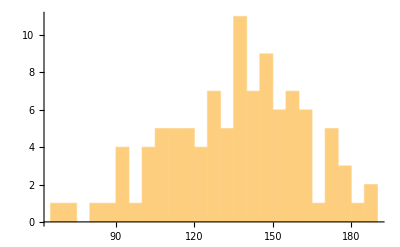

```mathematica
Histogram[myData,30]
```

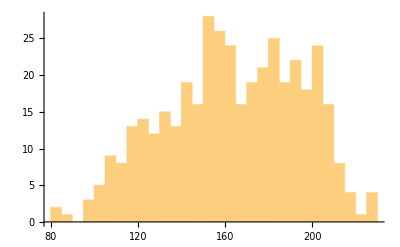

```mathematica
Histogram[#["speed"]&/@Select[Flatten@results,#["userId"]==471141&&#["speed"]!=0&],30,PlotRange->All]
```

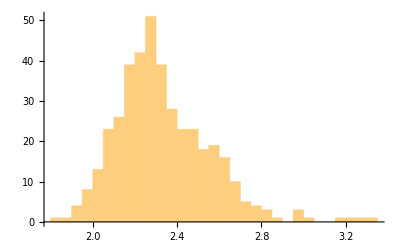

```mathematica
Histogram[#["keyLength"]&/@Select[Flatten@results,#["userId"]==471141&&#["speed"]!=0&],30,PlotRange->All]
```

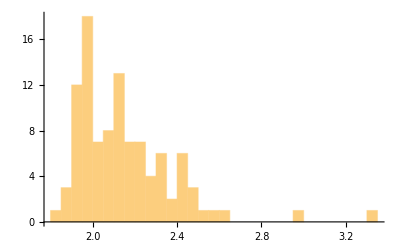

```mathematica
Histogram[#["keyLength"]&/@Select[Flatten@results,#["userId"]==471267&&#["speed"]!=0&],30,PlotRange->All]
```

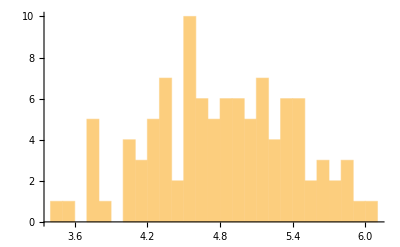

```mathematica
Histogram[#["keySpeed"]&/@Select[Flatten@results,#["userId"]==471267&&#["speed"]!=0&],30,PlotRange->All]
```